```mathematica
dataLab4 = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/4_Lab/table.csv"];

TableForm[dataLab4]

colLab41 = dataLab4[[All, 1]][[2 ;; 9]];
colLab42 = dataLab4[[All, 2]][[2 ;; 9]];
tolLab4 = dataLab4[[All, 3]][[2 ;; 9]];
dataTuple={colLab41, colLab42};
dataLab4Tuple = Transpose[dataTuple];
```

Mirror position (m) | Delay time (ns) | Uncertainty (ns) | Predicted Delay Time (ns) | Residuals (ns)
1.0732 | 25.6 | 0.1 | 25.7037 | -0.103719
1.3145 | 26. | 0.1 | 27.5117 | -1.51165
1.4669 | 28.8 | 0.1 | 28.6535 | 0.146496
1.6589 | 30.4 | 0.1 | 30.0921 | 0.307942
1.8621 | 32.2 | 0.1 | 31.6145 | 0.585472
2.059 | 34.4 | 0.1 | 33.0898 | 1.3102
2.34 | 35.4 | 0.1 | 35.1952 | 0.20482
3.0559 | 39.6 | 0.1 | 40.559 | -0.959039

```mathematica
(*Weighted Least-Squares Fit*)
```

```mathematica
sim=  Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{dataLab4Tuple,tolLab4}],1];
fit=LinearModelFit[sim,x,x]
Normal@ fit
```

FittedModel[17.6664+7.49033 x]

17.6664+7.49033 x

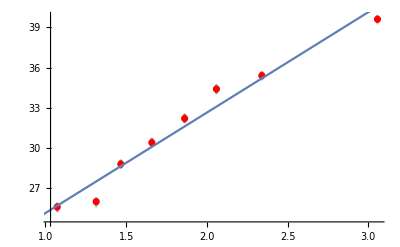
-Graphics-mirror position (m)delay time (ns)

```mathematica
s1 = Labeled[
Show[{
ListPlot[sim,PlotStyle->{Opacity[.25],Gray}],
ListPlot[dataLab4Tuple,PlotStyle->Red],
Plot[{fit[x]},{x,0,dataLab4Tuple[[-1,1]]},Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Red,Bold]]
}],
{"mirror position (m)", "delay time (ns)"},
{Bottom, Left},
RotateLabel->True
]
```

```mathematica
(*Least-Squares Fit*)
bestFitSlope[data_]:=Module[{lm,x},lm=LinearModelFit[data,{1,x},x];
First@Pick[lm["BestFitParameters"],lm["BasisFunctions"],x]];
```

```mathematica
lineData=Fit[dataLab4Tuple,{1,x},x];
val=Last[lineData];
val/. x->1
```

7.49245

```mathematica
(*Residual Plot*)
colLab43 = dataLab4[[All, 4]][[2 ;; 9]]; (*Predicted Delay Time*)
colLab44 = dataLab4[[All, 5]][[2 ;; 9]]; (*Residuals*)

lab4PlotPairErrs = {colLab41, colLab44};
lab4PlotPairErrsTuple = Transpose[lab4PlotPairErrs];

lab4PlotPairErrsWUncertainty = {colLab41, colLab44, tolLab4};
lab4PlotPairErrsWUncertaintyTuple = Transpose[lab4PlotPairErrsWUncertainty];
```

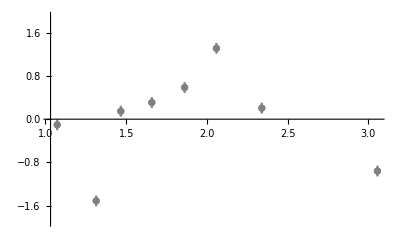
-Graphics-mirror position (m)delay time residual (ns)

```mathematica
Needs["ErrorBarPlots`"]
l1 = Labeled[
	Show[
	ListPlot[lab4PlotPairErrsTuple, PlotRange->{-1.9, 1.9}],     (*Note the Range*)
	Plot[lm[x],{x,0,12}],
	ErrorListPlot[lab4PlotPairErrsWUncertaintyTuple,PlotStyle->Gray]
   ],
{"mirror position (m)", "delay time residual (ns)"},
{Bottom, Left},
RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"graph_residual.png", l1, ImageResolution-> 200]
Export[NotebookDirectory[]<>"graph.png", s1, ImageResolution-> 200]
```

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/4_Lab/graph_residual.png

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/4_Lab/graph.png

```mathematica
c = 2/7.4903294083158745 * 10^9
```

```mathematica
2.6701095385465562*^8

(2.997 - 2.670) / 2.997 * 100
```

2.67011×10^8

10.9109